```mathematica
SetDirectory@NotebookDirectory[]
Get["MyPackage.wl"]
```

C:\Universita\MAGISTRALE\MasterThesis\Mathematica

```mathematica
ClearAll["Global`*"]
```

```mathematica
arrowcycle[]:= Line[x_]:>{Arrowheads[{0,0,0.05,0}],Arrow[x]}
```

```mathematica
scientstring[n_,dig_]:=ToString[ScientificForm[n,dig],TraditionalForm]
```

```mathematica
alldata=Import["ovalcell_data.m"]
```

<|cellVal→{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,w0→1/10,tp0→1/40000,tf0→1/100000,ϵ1max→0.05},tankVal→{d→5,Pt→50000,Vtank→1,Vftot→1,f→0.1},gasVal→{patm→101325,Tstd→288.15,γair→1.4,ρstdair→1.225,cv→717.2,cp→1.0042}|>

```mathematica
celldata=alldata["cellVal"]
```

{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,w0→1/10,tp0→1/40000,tf0→1/100000,ϵ1max→0.05}

-Graphics-

```mathematica
opts={GridLines->Automatic,GridLinesStyle->LightGray,LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize->12},AxesStyle->{FontFamily->"Times New Roman"},Frame->True};
```

```mathematica
data0={h0->10^-3,l0->10^-2};
```

```mathematica
solvegeom[h0_,l0_,pts_]:=Module[{θ0,R0,areaarc0,area,hvec,lcvec,Rtmp,Rvec,θvec},
If[NumericQ[h0]&&NumericQ[l0],
θ0=α0/.FindRoot[((h0-l0/α0(1-Cos[α0/2]))/.data0)==0,{α0,ArcCos[(2 h0)/l0/.data0]}];
R0=l0/θ0/.data0;
areaarc0=1/2 R0^2(θ0-Sin@θ0);
area=R lc(1-Cos[(l0-lc)/(2 R)])+R^2/2((l0-lc)/R-Sin[(l0-lc)/R]);
lcvec=LinSpace[0,l0-l0/3,pts]/.data0;
Rtmp={R0};
Rvec=Flatten@Table[Rtmp=R/.FindRoot[(area==areaarc0)/.lc->lcvec[[i]],{R,Rtmp}],{i,1,Length@lcvec}];
θvec=(l0-lc)/R/.{lc->lcvec,R->Rvec}/.data0;
hvec=R(1-Cos[θ/2])/.{R->Rvec,θ->θvec};
{hvec,lcvec,Rvec,θvec}]]
```

```mathematica
DrawCell[{hvec_,lcvec_,Rvec_,θvec_},idx_,{xbias_,{ybias_,tf0_}},initialcond_]:=Module[{initialgeom,inbias},
If[ybias!=0,inbias=(hvec[[1]]+tf0)ybias/(hvec[[idx]]+tf0),inbias=0];
If[initialcond==1,
initialgeom={Circle[{-lcvec[[1]]/2+xbias,-(Rvec[[1]]-hvec[[1]])+inbias},Rvec[[1]],{π/2,π/2+θvec[[1]]/2}],(*Initial upper part*)
Circle[{lcvec[[1]]/2+xbias,-(Rvec[[1]]-hvec[[1]])+inbias},Rvec[[1]],{π/2,π/2-θvec[[1]]/2}],
Circle[{lcvec[[1]]/2+xbias,Rvec[[1]]-hvec[[1]]+inbias},Rvec[[1]],{3π/2,3π/2+θvec[[1]]/2}],(*Inital lower part*)
Circle[{-lcvec[[1]]/2+xbias,Rvec[[1]]-hvec[[1]]+inbias},Rvec[[1]],{3π/2,3π/2-θvec[[1]]/2}]},initialgeom={}];
Graphics[{Darker@Red,Dashed,
initialgeom,
Thick,Dashing@None,
Circle[{-lcvec[[idx]]/2+xbias,-(Rvec[[idx]]-hvec[[idx]])+ybias},Rvec[[idx]],{π/2,π/2+θvec[[idx]]/2}],(*Upper part*)
Line[{{-lcvec[[idx]]/2+xbias,hvec[[idx]]+ybias},{lcvec[[idx]]/2+xbias,hvec[[idx]]+ybias}}],
Circle[{lcvec[[idx]]/2+xbias,-(Rvec[[idx]]-hvec[[idx]])+ybias},Rvec[[idx]],{π/2,π/2-θvec[[idx]]/2}],(*Lower part*)
Circle[{lcvec[[idx]]/2+xbias,Rvec[[idx]]-hvec[[idx]]+ybias},Rvec[[idx]],{3π/2,3π/2+θvec[[idx]]/2}],
Line[{{-lcvec[[idx]]/2+xbias,-hvec[[idx]]+ybias},{lcvec[[idx]]/2+xbias,-hvec[[idx]]+ybias}}],
Circle[{-lcvec[[idx]]/2+xbias,Rvec[[idx]]-hvec[[idx]]+ybias},Rvec[[idx]],{3π/2,3π/2-θvec[[idx]]/2}]}]
]
```

```mathematica
geom0=solvegeom[h0/.data0,l0/.data0,100];
```

```mathematica
Equal@@Table[ArcLength[Circle[{0,0},geom0[[3]][[i]],{0,geom0[[4]][[i]]}]]+geom0[[2]][[i]],{i,1,Length@hvec}]
```

True

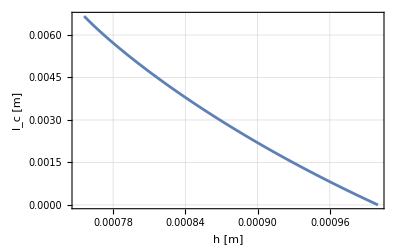
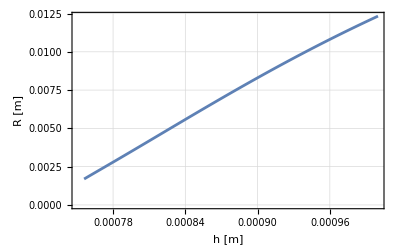

```mathematica
Row[{ListPlot[Transpose@{geom0[[1]],geom0[[2]]},FrameLabel->{"h [m]", "l_c [m]"},Joined->True,Evaluate@opts],
ListPlot[Transpose@{geom0[[1]],geom0[[3]]},FrameLabel->{"h [m]", "R [m]"},Joined->True,Evaluate@opts]}]
```

### Test geometries

```mathematica
data0test={h0-> 0.5 10^-3,l0->0.5 10^-2};
```

```mathematica
h0range=h0{0.5,1,1.5}/.data0test//N;
l0range=l0{0.5,1,1.5}/.data0test//N;
h0strings=Table[StringJoin["h_0 = ",scientstring[h0range[[i]],3]," [m]"],{i,1,Length@h0range}]
l0strings=Table[StringJoin["l_0 = ",scientstring[l0range[[i]],3]," [m]"],{i,1,Length@l0range}]
```

{h_0 = 2.5×10^-4 [m],h_0 = 5.×10^-4 [m],h_0 = 7.5×10^-4 [m]}

{l_0 = 2.5×10^-3 [m],l_0 = 5.×10^-3 [m],l_0 = 7.5×10^-3 [m]}

```mathematica
geomhl=Table[solvegeom[h0range[[i]],l0range[[j]],100],{i,1,Length@h0range},{j,1,Length@l0range}];(*geomhl[[i,j]] -> h0range[[i]],l0range[[j]]*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Manipulate[{
Row[Table[Block[{xlim=0.95l0range[[1]],ylim=-1.2h0range[[i]]},Show[DrawCell[geomhl[[i,1]],idx,{0,{0,0}},dash],PlotLabel->Column[{h0strings[[i]],l0strings[[1]]}],LabelStyle->{Black,Bold},Axes->True,AspectRatio->(3h0range[[i]])/l0range[[3]],ImageSize->400,PlotRange->{{-xlim,xlim},{-ylim,ylim}}]],{i,1,3}]],
Row[Table[Block[{xlim=0.95l0range[[2]],ylim=-1.2h0range[[i]]},Show[DrawCell[geomhl[[i,2]],idx,{0,{0,0}},dash],PlotLabel->Column[{h0strings[[i]],l0strings[[2]]}],LabelStyle->{Black,Bold},Axes->True,AspectRatio->(3h0range[[i]])/l0range[[3]],ImageSize->400,PlotRange->{{-xlim,xlim},{-ylim,ylim}}]],{i,1,3}]],Row[Table[Block[{xlim=0.95l0range[[3]],ylim=-1.2h0range[[i]]},Show[DrawCell[geomhl[[i,3]],idx,{0,{0,0}},dash],PlotLabel->Column[{h0strings[[i]],l0strings[[3]]}],LabelStyle->{Black,Bold},Axes->True,AspectRatio->(3h0range[[i]])/l0range[[3]],ImageSize->400,PlotRange->{{-xlim,xlim},{-ylim,ylim}}]],{i,1,3}]]
}
,{idx,1,100,1},{{dash,1,"Undeformed"},{0,1}}]
```

### Double cell unit

```mathematica
data0={h0->h0range[[2]],l0->l0range[[2]]};
cellidx=2;
```

```mathematica
cell=solvegeom[h0/.data0,l0/.data0,1000];
hvec=cell[[1]];lcvec=cell[[2]];Rvec=cell[[3]];θvec=cell[[4]];
```

```mathematica
Manipulate[Block[{ylim=4(h0range[[cellidx]]),xlim=l0range[[cellidx]],tf0=tf0/.celldata},
Show[
Table[DrawCell[cell,idx,{0,{2(i-1)(cell[[1,idx]]+tf0),tf0}},dash],{i,1,2,1}],
PlotLabel->Row[{h0strings[[cellidx]],Spacer@10,l0strings[[cellidx]]}],Evaluate@opts,FrameLabel->{"x [m]","y [m]"},Axes->True,ImageSize->700,PlotRange->{{-xlim,xlim},{-0.5ylim,ylim}}]],{idx,1,Length@cell[[1]],1},{{dash,1,"Undeformed"},{0,1}}]
```

```mathematica
numdlch=Differences[lcvec]/Differences[hvec];
```

```mathematica
hveceff=hvec[[1;;Length@numdlch]];
```

```mathematica
CC=(((ϵp w0 lc[h])/(2 tp0))^-1+((ϵf w0 lc[h])/tf0)^-1)^-1//Simplify;
dCCh=D[CC,h]
```

(w0 ϵf ϵp lc'[h])/(2 tp0 ϵf+tf0 ϵp)

```mathematica
Cvec=CC/.celldata/.lc[h]->lcvec;
```

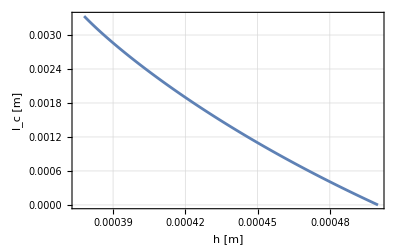
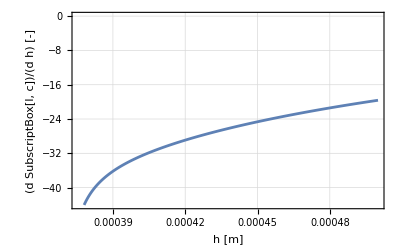

```mathematica
Row[{
Show[ListPlot[Transpose[{hvec,lcvec}],Joined->True,Evaluate@opts,FrameLabel->{"h [m]","l_c [m]"}]],
ListPlot[Transpose[{hveceff,numdlch}],Joined->True,Evaluate@opts,FrameLabel->{"h [m]","(d SubscriptBox[l, c])/(d h) [-]"}]}]
```

```mathematica
GeometricStep
```

GeometricStep

```mathematica
Vrange=Range[0,6000,2000];
Vstrings=Table[StringJoin["V = ",scientstring[Vrange[[i]],3]," [V]"],{i,1,Length@Vrange}];
```

```mathematica
F=-V^2/2 D[CC,h];
```

```mathematica
Fcell=F/.lc'[h]->numdlch/.celldata;
```

```mathematica
UelFh=CumTrapz[hvec[[1;;Length@Fcell]],Fcell/.V->Last@Vrange];
```

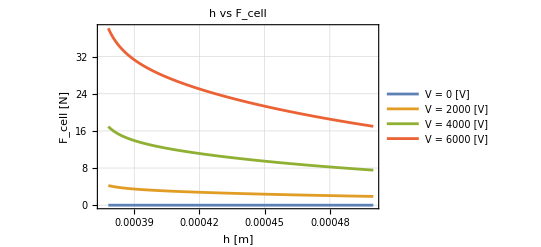
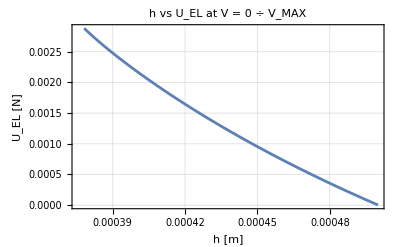

```mathematica
Row[{ListPlot[Table[Transpose[{hveceff,Fcell/.V->Vrange[[i]]}],{i,1,Length@Vrange}],Joined->True,Evaluate@opts,FrameLabel->{"h [m]","F_cell [N]"},PlotLabel->"h vs F_cell",PlotLegends->Vstrings],
ListPlot[Transpose[{hveceff[[1;;Length@UelFh]],UelFh}],Joined->True,Evaluate@opts,FrameLabel->{"h [m]","U_EL [N]"},PlotLabel->"h vs U_EL at V = 0 ÷ V_MAX"]}]
```

#### Q-V plot

C = Q / V

```mathematica
Cvec=CC/.celldata/.lc[h]->lcvec;
```

```mathematica
{Cmin=Cvec[[1]],Cmax=Last@Cvec}
```

{0.,1.60243×10^-10}

```mathematica
Vmaxdef=LinSpace[0,Last@Vrange,Length@Fcell];
```

```mathematica
Qmaxdef=Cmax Vmaxdef;
```

```mathematica
Vmindef=LinSpace[0,Last@Vrange,Length@Fcell];
```

```mathematica
Qmindef=Cmin Vmindef;
```

```mathematica
QVmax=LinSpace[0,Last@Qmaxdef,Length@Fcell];
```

```mathematica
Vmaxvec=ConstantArray[Last@Vrange,Length@Fcell];
```

```mathematica
QVpl[style_]:=ListPlot[{
Transpose[{Qmindef,Vmindef}],Transpose[{Qmaxdef,Vmaxdef}],Transpose[{QVmax,Vmaxvec}]},PlotStyle->style,
Joined->True,FrameLabel->{"Q [A]","V [V]"},PlotLabel->"Q vs V",Evaluate@opts,PlotLegends->{"Min. def.","Max. def.","V_MAX"}]
```

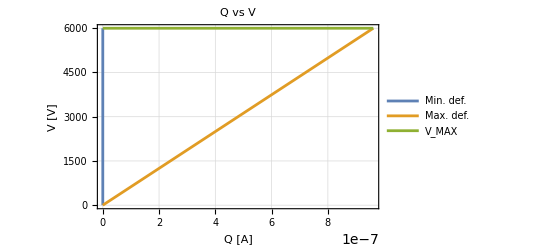

```mathematica
QVpl[Automatic]
```

```mathematica
UelQV=CumTrapz[QVmax,Vmaxvec]-CumTrapz[Qmaxdef,Vmaxdef];
```

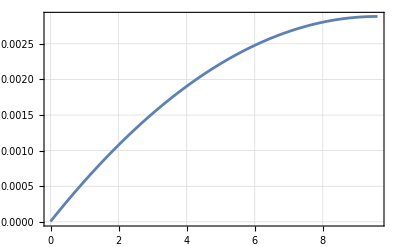

```mathematica
ListPlot[Transpose[{QVmax[[1;;Length@UelQV]],UelQV}],Joined->True,PlotRange->All,Evaluate@opts]
```

#### Q-V plots in working condition

```mathematica
FintVmax=Interpolation[Transpose[{hveceff,Fcell/.V->Last@Vrange}]];
FintVmin=Interpolation[Transpose[{hveceff,Fcell/.V->Vrange[[1]]}]];
```

```mathematica
lcint=Interpolation[Transpose[{hvec,lcvec}]];
```

```mathematica
hdom=FintVmax["Domain"][[1]]
```

{0.000378054,0.0005}

```mathematica
Ch=CC/.celldata/.lc[h]->lcint[h]
```

4.80728×10^-8 InterpolatingFunction[…][h]

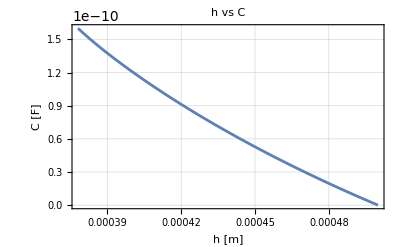

```mathematica
Plot[Ch,{h,## & @@ hdom},Evaluate@opts,FrameLabel->{"h [m]","C [F]"},PlotLabel->"h vs C"]
```

```mathematica
fixedhpath[n_,hleft_,hright_,FintV0_,FintVmax_,Vrange_]:=Module[{hA,hB,hC,hD,hrangeAB,hrangeBC,hrangeCD,hrangeDA,VAB,VBC,VCD,VDA,CAB,CBC,CCD,CDA,QAB,QBC,QCD,QDA},
hA=hright;
hB=hleft;
hC=hB;
hD=hA;
hrangeAB=LinSpace[hA,hB,n];hrangeBC=ConstantArray[hB,n];hrangeCD=LinSpace[hC,hD,n];hrangeDA=ConstantArray[hA,n];
VAB=ConstantArray[Vrange[[1]],n];VBC=LinSpace[Vrange[[1]],Last@Vrange,n];VCD=ConstantArray[Last@Vrange,n];VDA=LinSpace[Last@Vrange,Vrange[[1]],n];
CAB=Ch/. h->hrangeAB;CBC=Ch/.h->hrangeBC;CCD=Ch/.h->hrangeCD;CDA=Ch/.h->hrangeDA;
QAB=CAB VAB;QBC=CBC VBC;QCD=CCD VCD;QDA=CDA VDA;
{{{hA,FintV0[hA]},{hB,FintV0[hB]},{hC,FintVmax[hC]},{hD,FintVmax[hD]}},{hrangeAB,hrangeBC,hrangeCD,hrangeDA},{VAB,VBC,VCD,VDA},{CAB,CBC,CCD,CDA},{QAB,QBC,QCD,QDA}}]
```

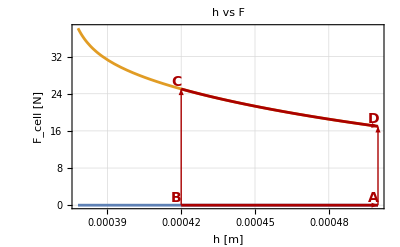
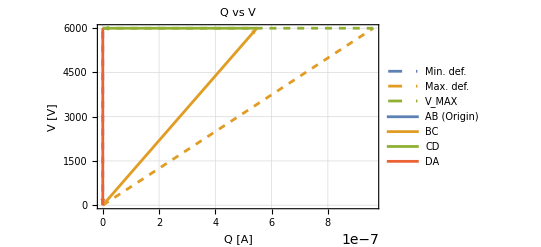

```mathematica
Module[{hleft=0.00042,hright=h0/.data0,xtol=0.000002,ytol=1.5},
{ptsh,hrangesh,Vrangesh,Crangesh,Qrangesh}=fixedhpath[100,hleft,hright,FintVmin,FintVmax,Vrange];
Row[{
Show[
Plot[{FintVmin[h],FintVmax[h]},{h,hdom[[1]],hdom[[2]]},Evaluate@opts,FrameLabel->{"h [m]","F_cell [N]"},PlotLabel->"h vs F"],
Plot[{FintVmin[h]},{h,hleft,hright},PlotStyle->Darker@Red] /.MidArrow[-1],
Plot[{FintVmax[h]},{h,hleft,hright},PlotStyle->Darker@Red] /.MidArrow[1],
Graphics[{Thick,Darker@Red,
Line[{{hleft,FintVmin@hleft},{hleft,FintVmax@hleft}}]/.MidArrow[1],
Line[{{hright,FintVmin@hright},{hright,FintVmax@hright}}]/.MidArrow[-1],
MapThread[Text[Style[#1,{Bold,14,FontFamily->"Consolas"}],#2+{-xtol,ytol}]&,{{"A","B","D","C"},Flatten[Table[{j,i[j]},{i,{FintVmin,FintVmax}},{j,{hright,hleft}}],1]}]}]
],
Show[
QVpl[Dashed],
ListPlot[Table[Transpose[{Qrangesh[[i]],Vrangesh[[i]]}],{i,1,Length@Qrangesh}],Joined->True,PlotLegends->{"AB (Origin)","BC","CD","DA"},Evaluate@opts]/.MidArrow[1]]}]

]
```

### Stack

```mathematica
Manipulate[Block[{lim=l0/.data0,tf0=tf0/.celldata},
Show[Table[DrawCell[cell,idx,{(-Floor[Nc/2]+j-1) l0/.data0,{2(i-1)(hvec[[idx]]+tf0),tf0}},dash],{j,1,Nc},{i,1,Ns}],
PlotLabel->Row[{h0strings[[cellidx]]," ",l0strings[[cellidx]]}],Evaluate@opts,ImageSize->1100,LabelStyle->{Black,Bold},Axes->True,PlotRange-> 4(l0/.data0){{-1,1},{-0.1,0.3}}]]
,{{dash,1,"Undeformed"},{0,1}},
Row[{Control[{{idx,1,"h"},1,Length@cell[[1]],1}],Dynamic@hvec[[idx]],Spacer@10,Control[{Nc,1,7,1}],Spacer@10,Control[{{Ns,5},1,5,1}]}]]
```